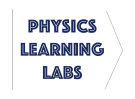
# -Graphics- Lab 2 - Projectile Kinematics

In this lab we will launch metal spheres, determine their range as a function of θ, and use the theoretical equation to estimate their initial velocity.

## Background

### Theory

R=v_0^2/g sin(2θ)

### Apparatus

Keep safety glasses on when operating the projectile launcher. 
Your TA will instruct you when appropriate to remove the glasses.

Only use short range setting (1st click)

Swiftly and firmly engage/disengage the plunger to release the projectile. Be consistent!

Do not remove launcher from frame

View the hanging “bob” to determine angle, making sure it can hang freely

Be sure classmates and objects are out of range before firing

Tape down the measuring tape and landing paper to the table

## Experiment

### Data Collection

Measure the range (in meters) for ten angles, θ = {20, 25, 30, 35, 40, 45, 50, 55, 60, 65, 70}

Keep your method simple and consistent. It is easiest to make a reference measurement first (a point with known distance), then measure the change in distance from this point.

Record your measurements as a list in the form {{θ_1, R_1}, {θ_2, R_2}, ...., {θ_10, R_10}} and store within variable mydata

```mathematica
mydata =
```

Use ListPlot to plot mydata. Include appropriate axis labels (distance in units of meters). Add the option PlotStyle→Red and store your plot as variable myplot.

```mathematica
myplot=ListPlot[mydata,AxesLabel->{"θ °", "R (m)"},PlotStyle->Red]
```

### Linear Fitting

As to be expected from the range equation, Eq. (1), your data probably does not look linear. Theory suggests it should follow a function like v_0^2/g sin(2θ). However, we do not know the value of the constant v_0. One way to determine the initial velocity is to turn our non-linear plot into a linear plot. To do this, we choose appropriate y and x axis variables that allow our equation to be linear. In the case of our range equation,

R=v_0^2/g sin(2θ)

the dependent y variable is the range R and the independent x variable is θ. To make this equation linear, let’s do a substitution

sin(2θ)=x

Now our equation looks like

R=v_0^2/g x

Since  v_0^2/g is just a constant, our new equation takes the linear form y=mx. Hence, if we plot R(x) the graph will be linear, and since x=sin(2θ) this means we need to really just plot R vs. sin(2θ). Initially our x axis ranged from θ=0 to θ=90. Our new axis will range from x=0 to x=1.

Now we need to modify our list so that the x variable is now sin(2θ) instead of θ, i.e.
{{θ_1, R_1}, {θ_2, R_2}, ...., {θ_10, R_10}} →   {{sin(2 θ_1), R_1}, {sin(2 θ_2), R_2}, ...., {sin(2 θ_10), R_10}},

With the Table[] function, create a list of data labeled lineardata by making the above transformation upon each element of θ. Don't forget to convert to radians. Ask your TA for help if needed.

```mathematica
lineardata = Table[{Sin[2 π/180 mydata[[i]][[1]]],mydata[[i]][[2]]},{i,1,Length[mydata]}];
```

Use ListPlot to plot lineardata. Include appropriate axis labels, add the option PlotStyle→Red, and store your plot as variable linearplot.

```mathematica
linearplot =ListPlot[lineardata,PlotStyle->Red,AxesLabel->{"Sin(2θ)","R (m)"},PlotRange->{{0,1.1},{0,All}}]
```

### Fitting the Data

In order to fit this data with a straight line, we need to determine the linear function that best approximates the data.

Use the slider to find the slope of the line of best fit.

```mathematica
Manipulate[Show[linearplot, Plot[m x,{x,0,2}]],{m,0,1,0.001,Appearance->"Open"},SaveDefinitions->True]
```

## Analysis

Display the graph of your experimental results of R(θ)

Present an analysis of the graph. What is the relationship between range and angle? What point(s) correspond to the smallest range? Approximately what angle produces the maximum range?

Display the graph of R vs. sin(2θ) including the linear fit

Present an analysis of the above graph, including a comparison of the (theoretical) linear fit to the experimental data

In the process of linear fitting, we brought our data into the form y=mx. What does y represent? What about x? What was the purpose of plotting R vs. sin(2θ) ?

When we plotted the linear function, x ranged from [0,1]. Why?

Are there any two angles that will produce approximately the same range?

What is the value of the slope of the linear fit function? What are the units?

Comparing the slope to the range equation, what physical quantity does the slope represent?

Assuming  g=9.81 m/s^2, determine the value of v_0, the initial velocity

Summarize this lab, What were the objectives? What did you find? How did your results compare to the theoretical expectation? Can you account for any presumable discrepancies in the data?

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).